# The positroids Package -Graphics-

## Setup and Initialization

The positroids package can be loaded by the following (so long as “positroids.m” is in the same directory as the notebook)

```mathematica
SetDirectory[NotebookDirectory[]];
<<positroids.m
```

-Graphics-
Grassmannian Positroids, Plabic Graphs,
& Scattering Amplitudes in N=4 SYM
Jacob L. Bourjaily, 2012

If the file “positroids.m” is copied to your Mathematica’s “Application” directory,

```mathematica
FileNameJoin[{$UserBaseDirectory,"Applications"}]
```

via the command,

```mathematica
If[Not[FileExistsQ[FileNameJoin[{$UserBaseDirectory,"Applications","positroids.m"}]]],CopyFile[FileNameJoin[{NotebookDirectory[],"positroids.m"}],FileNameJoin[{$UserBaseDirectory,"Applications","positroids.m"}]]];
```

then “<<positroids.m” can be used in any notebook without any further initialization.

## Basic Operations

### Labeling positroid configurations

#### Decorated permutations labeling positroids

The positroids package uses permutations s—given by the list of the images {s[1],...s[n]}—to label a each configuration in the positroid stratification of G(k,n).

```mathematica
egPerm=random[Permutations[Range[8]]]
```

The images of s which label the permutation should be defined according to the convention:

a⩽σ[a]⩽a+n

Although a considerable abuse of notation, the function of positroids which makes sure a permutation is written according to this convention is “decorate[perm_]”:

```mathematica
egPerm=decorate[egPerm]
```

#### Associating each decorated permutation with a configuration in G(k,n)

Each permutation of length n labels a positroid cell in G(k,n) where k is given by:

```mathematica
permutationK[egPerm]
```

We can get an idea of the geometry of the stratum labeled by a permutation via the function “permtoGeometry[perm_]” which gives an array listing the chains of consecutive spanning spaces of rank 1,2,... in successive rows:

```mathematica
permToGeometry[egPerm]
```

#### The dimensionality of a positroid stratum

The dimension of the stratum labelled by the permutation can be computed using the function dimension[perm_]:

```mathematica
dimension[egPerm]
```

#### Matrix representatives of positroids

And a matrix-representative of the positroid cell labeled by the permutation (in terms of canonical coordinates) is generated by the function “permToMatrix[perm_]”:

```mathematica
egMat=permToMatrix[egPerm];
nice@%
```

Going in the other direction: if given a matrix, the positroid stratum that contains it can be found using the function
“matToPerm[matrix_]”:

```mathematica
matToPerm[egMat]
%===egPerm
```

#### Positivity of canonical coordinates for positroids

The ‘canonical coordinates’ which parameterize this matrix-representative are automatically ‘positive’ coordinates: if all coordinates take on random, positive values, then all ordered-minors are positive.

```mathematica
egMat=permToMatrix[egPerm];
positiveQ[egMat]
```

You can also verify this yourself as follows. The function explicify[exprn_] fixes all coordinates to take-on random values—by default, random positive values.

```mathematica
explicitMat=explicify[egMat];
nice@%
```

```mathematica
Sign[Det[explicitMat[[All,#]]]]&/@Subsets[Range[Length[egPerm]],{permK[egPerm]}]
```

Notice that all non-vanishing minors are positive. (Sign[] returns 1 if its argument is positive, 0 if it vanishes, -1 if negative.)

### The positroid stratification

#### The boundaries of positroid configurations

The positroid stratification is defined by the covering relations generated by the boundary operator “∂”. 
We can explore this using any strata—for instance, a 20-dimensional strata of G(6,12). 
Such a random cell can be obtained using the function “randomCell[n_,k_,dim_]”:

```mathematica
egPerm=randomCell[12,6,20]
dimension[egPerm]
```

The complete list of boundary-elements of the cell labelled by egPerm is generated by the function “boundary[perm_]”:

```mathematica
egBoundary=boundary[egPerm]
dimension/@%
```

#### Checking that “boundary[]” does in fact define a “boundary” (namely, that it squares to zero).

We can check that “∂^2 =0” (mod 2) by joining the boundaries of each of these boundary elements,

```mathematica
egBoundarySquared=Join@@(boundary/@egBoundary);
Length@%
```

and deleting any element that occurs an even number of times using the function “mod2[list_]”:

```mathematica
mod2[egBoundarySquared]
```

#### Inverse boundaries

The function “inverseBoundary[perm_]” works similarly: listing all the cells whose boundary contains perm:

```mathematica
egInverseBoundary=inverseBoundary[egPerm]
```

It is easy to check that the boundaries of all cells in “egInverseBoundary” include the cell labelled by egPerm:

```mathematica
intersection@@(boundary/@egInverseBoundary)
%==={egPerm}
```

#### Exempli Gratia: checking the Euler characteristic of G_+(k,n):

The generic (top-dimensional) positroid configuration in G(k,n) is always labelled by {1+k,...,n+k}. 
For example, consider the top-cell of G(2,4):

```mathematica
topCellPerm=Range[4]+2;
```

By taking successive boundaries, we can generate all the cells in the positroid stratification:

```mathematica
completePositroidStrata=FixedPointList[DeleteDuplicates[Join@@(boundary/@#)]&,{topCellPerm}][[1;;-3]];
dimensionList=dimension/@#&/@%
```

That is, we have:

```mathematica
Grid[{Length[#],ToString[#[[1]]]<>"-dimensional cells"}&/@dimensionList,Alignment->Left]
```

From this data, we can compute the Euler characteristic as follows:

```mathematica
(Range[Length[dimensionList]]/.{x_Integer:>If[OddQ[x],1,-1]})*Reverse[Length/@dimensionList]
Total[%]
```

We can compare this the results of a purely combinatorial computation using eulerCharacteristicTable[n_,k_]:

```mathematica
eulerCharacteristicTable[Length[topCellPerm],permK[topCellPerm]]
```

The above example can easily be modified to test any G(k,n):

```mathematica
topCellPerm=With[{n=6,k=3},Range[n]+k];
completePositroidStrata=FixedPointList[DeleteDuplicates[Join@@(boundary/@#)]&,{topCellPerm}][[1;;-3]];
dimensionList=dimension/@#&/@%;
Column@{Row[{"The positroid stratification of G(",permK[topCellPerm],",",Length[topCellPerm],") includes:"}],Row[{Spacer[50],(Grid[{Length[#],ToString[#[[1]]]<>"-dimensional cells"}&/@dimensionList,Alignment->Left])}],"and has an Euler characteristic computed to be:",Row[Join[{(Range[Length[dimensionList]]/.{x_Integer:>If[OddQ[x],1,-1]}).Reverse[Length/@dimensionList],"="},Riffle[Reverse[Length/@dimensionList],(Range[2,Length[dimensionList]]/.{x_Integer:>If[OddQ[x],"+","-"]})]],Spacer[1]]}
```

We can compare this the results of a purely combinatorial computation using eulerCharacteristicTable[n_,k_]:

```mathematica
eulerCharacteristicTable[Length[topCellPerm],permK[topCellPerm]]
```

## Drawing On-Shell (Plabic) Graphs

### Basic Graph Drawing

#### The function “plabicGraph[perm_,options___]”

A representative reduced graph whose left-right path is given by any permutation can be generated by the function
“plabicGraph[perm_]”. 

For examplee, the top-cell of G(2,4) is labelled by the permutation {3,4,5,6}; 
a representative plabic graph for this cell can be drawn using:

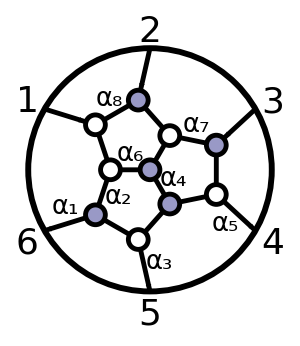

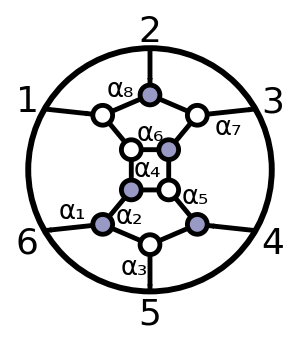

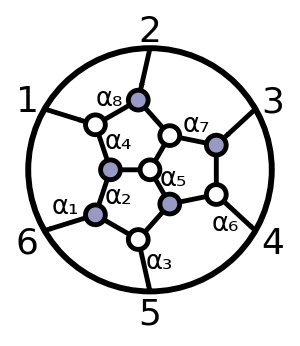

{{0,1,α[2]+α[4]+α[6],α[2] α[3],0,0},{0,0,1,α[3],α[1],α[1] α[8]},{α[7],α[5],α[5] α[6],0,0,1}}

(0 | 1 | α_2+α_4+α_6 | α_2 α_3 | 0 | 0
0 | 0 | 1 | α_3 | α_1 | α_1 α_8
α_7 | α_5 | α_5 α_6 | 0 | 0 | 1)

(1 | α_4+α_6+α_8 | (α_4+α_6) α_7 | α_4 α_5 | 0 | 0
0 | 1 | α_7 | α_2+α_5 | α_2 α_3 | 0
0 | 0 | 0 | 1 | α_3 | α_1)

(1 | α_4+α_8 | α_4 α_5+α_4 α_7 | α_4 α_5 α_6 | 0 | 0
0 | 1 | α_2+α_5+α_7 | (α_2+α_5) α_6 | α_2 α_3 | 0
0 | 0 | 1 | α_6 | α_3 | α_1)

```mathematica
egPerm1 = {4,5,6,8,7,9};
egPerm2 ={3,5,6,7,8,10};
egPerm3 ={4,6,5,7,8,9};
resetGraphDefaults;
plabicGraph[egPerm1,chainOption->0,directed-> True,edgeLabels-> True]
plabicGraph[egPerm2,chainOption->0,directed-> True,edgeLabels-> True]
plabicGraph[egPerm3,chainOption->0,directed-> True,edgeLabels-> True]
egMat=permToMatrix[egPerm1]
nice@egMat
egMat2=permToMatrix[egPerm2];
nice@egMat2
egMat3=permToMatrix[egPerm3];
nice@egMat3
```

```mathematica
matrixToPerm[{{1,Subscript[α, 1],0,0,0,Subscript[α, 2]},{0,Subscript[α, 6],1,Subscript[α, 5],0,Subscript[α, 6] Subscript[α, 7]},{0,Subscript[α, 6] Subscript[α, 8],0,Subscript[α, 4],1,Subscript[α, 3]+Subscript[α, 6] Subscript[α, 7] Subscript[α, 8]}}]
```

{4,6,5,7,8,9}

#### Drawing left-right path permutations

The fact that this plabic graph is associated with the corresponding permutation via its left-right paths can be seen by including the optional argument LRpaths→“All” as follows:

```mathematica
plabicGraph[egPerm,LRpaths->"All"]
```

Only those left-right paths which begin at legs {i,...,j} can be drawn by instead using the option LRpaths→{i,...,j} as in:

```mathematica
{plabicGraph[egPerm,LRpaths->{1}],
plabicGraph[egPerm,LRpaths->{2,4}],
plabicGraph[egPerm,LRpaths->{}]}
```

#### Indicating perfect-orientations for representative graphs

The representative graph generated by “plabicGraph” follows from a specific BCFW-decomposition of the permutation, and so always endows the graph with a perfect orientation. Such a perfect orientation is made visible using the option directed→True:

```mathematica
plabicGraph[egPerm,directed->True]
```

#### The underlying BCFW-bridge decomposition and its corresponding coordinates

In addition to endowing each graph with a perfect orientation, the BCFW-decomposition underlying “plabicGraph[perm_]” also endows the graph with canonical, BCFW-coordinates, whcih can be seen using the option edgeLabels→True:

```mathematica
plabicGraph[egPerm,edgeLabels->True]
```

Aside: the BCFW bridge-decomposition which underlies the output of “plabicGraph[perm_]” also underlies the generation of matrix-representatives of the positroid cell labelled by perm:

```mathematica
egMat=permToMat[egPerm];
nice[egMat]
```

Using this representative, it is easy to express any the minor in terms of the bridge coordinates:

```mathematica
explicitMinorsFromMatrix={m@@#,Det[egMat[[All,#]]]}&/@Subsets[Range[Length[egPerm]],{permK[egPerm]}];
Grid[nice/@%,Alignment->Left]
```

It is a highly non-trivial fact, however, that each BCFW-bridge coordinate itself can be written as a ratio of monomials of the minors of the matrix; this remarkable fact is encoded in the function “bridgeToMinors[perm_]” which generates the claimed correspondence:

```mathematica
nice/@bridgeToMinors[egPerm]
```

We can explicitly verify that the output of “birdgeToMinors[]” is correct by replacing the minors appearing in its output by those computed explicitly above—as encoded above in “explicitMinorsFromMatrix”:

```mathematica
nice/@(bridgeToMinors[egPerm]/.(Rule@@@explicitMinorsFromMatrix))
```

#### Resetting options for plabicGraph[]

By default, the function “plabicGraph[perm_,options___]” remembers the last options used until the length of perm is changed. 
And so, if we choose a random other cell in G(2,4), plabicGraph[perm_] will use the options established above:

```mathematica
plabicGraph[randomCell[4,2,3]]
```

The default options can be restored using the function “resetGraphDefaults”:

```mathematica
resetGraphDefaults;
plabicGraph[randomCell[4,2,3]]
```

#### Labeling faces and denoting face variables

The positroid call corresponding to a particular graph can be naturally described in terms of face variables. 
These can be indicated on the graph via the option faceLabels→True:

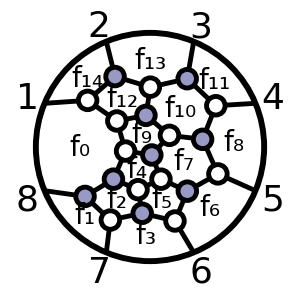

```mathematica
plabicGraph[egPerm,faceLabels->True]
```

These face labels are ordered according to the particular BCFW-bridge decomposition used to generate the graph (see documentation). 
These face variables can be thought of as “flux” computed in terms of edge variables:

```mathematica
Row[{plabicGraph[egPerm]," ⟺ ",plabicGraph[egPerm,faceLabels->False,directed->True,edgeLabels->True]}]
```

Using the correspondence between BCFW-bridge coordinates and minors of the matrix,

```mathematica
nice/@bridgeToMinors[egPerm]
```

we can express these face-variables directly in terms of the minors of the matrix as well. 
This is known as the “X”-variable labels—whcih can be drawn using the option faceLabels→“X”:

```mathematica
resetGraphDefaults; 
plabicGraph[egPerm,faceLabels->"X"]
```

$Aborted

Another set of face-variables (not directly associated with the minors any matrix-representative of the configuration) are called the “A”-variables. These can be drawn using the option faceLabels→“A”:

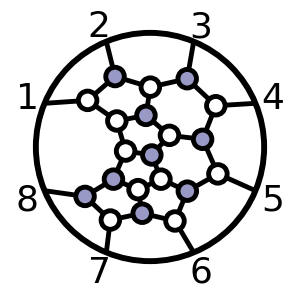

```mathematica
plabicGraph[egPerm,faceLabels->"A"]
```

#### Alternative graphs for a given permutation

The representative graphs generated by plabicGraph[perm_] are generated according to some specific BCFW-decomposition of the permutation perm, and different schemes generate different representative graphs. 

All recursion schemes depend on the ordering of legs, and by default this ordering is taken to be 1<⋯<n. But of couse, any leg could be taken as “first”.
The optional argument rotation->a instructs plabicGraph[] to draw the graph according to a scheme where leg (1-a) is taken to be “first”. 
This can in practice be used to generate many seemingly inequivalent representative grpahs for any particular permutation:

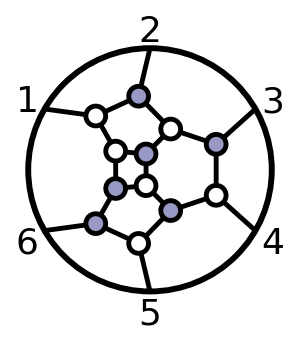
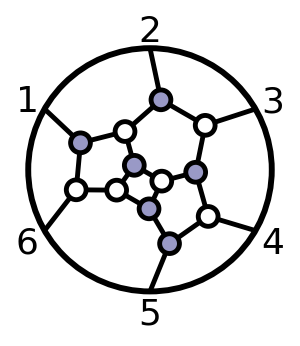
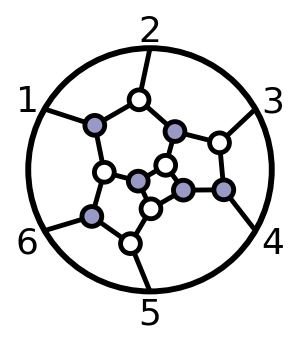
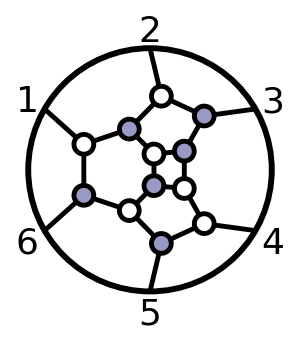
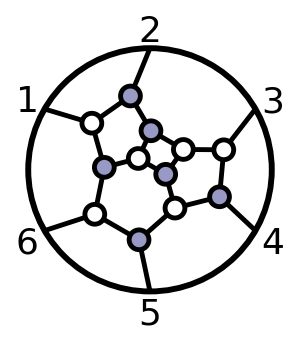
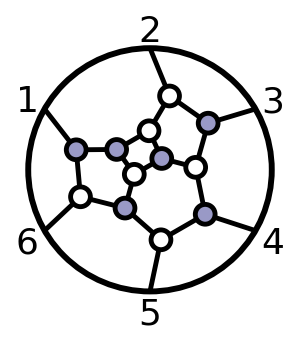
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
egPerm=randomCell[6,3,9];
plabicGraph[egPerm,rotation->#]&/@Range[0,7]
```

### Exempli Gratia: Elementary and Advanced Examples of plabicGraph[]

#### Permutations with fixed-points/graphs with “hanging” legs

Fixed-points of permutations are differentiated according to whether σ[a]=a or σ[a]=a+n. Such “decorations” allow us to distinguish among (n
k) possible “trivial” permutations—for which the distinction between σ[a]=a and σ[a]=a+n is easily understood:

```mathematica
egPerm=randomCell[6,3,0];
egGraph=plabicGraph[egPerm,LRpaths->"All"];

Column[{Row[{"The positroid labelled by: ",(egPerm/.{x_Integer:>Style[x,If[x>Length[egPerm],Red,Blue]]})}],"        corresponds to the following:",Grid[{{egGraph,nice[permToMat[egPerm]],permToGeometry[egPerm]},{"graph","matrix rep.","geometry"}}]}]
```

The positroid labelled by: {1,8,3,10,11,6}
        corresponds to the following:
-Graphics- | (0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0) | ((2)(4)(5)
(2,4)(4,5)(5,2))
graph | matrix rep. | geometry

#### Drawing on-shell graphs for scattering amplitudes:

The function “treeContour[n_,k_]” returns the permutations labeling cells generated by the BCFW-recursion relations. Representative graphs can easily be generated for these as in the following example:

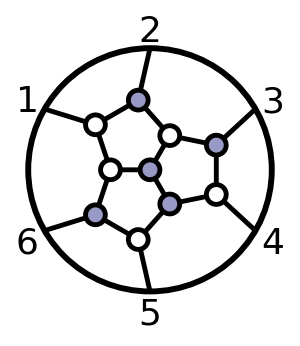
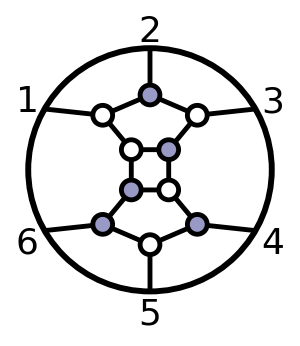
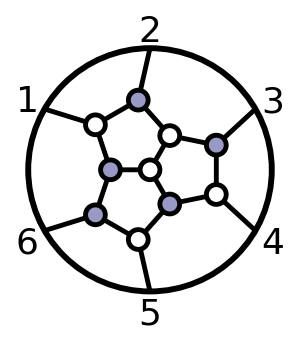

```mathematica
plabicGraph/@treeContour[6,3]
```

#### More complex examples of graphs and possible options for plabicGraph[]

There are many more options available to alter the graph produced by plabicGraph[]; these are described more fully in the associated documentation. 
Below, we give several examples which vary these options to illustrate the scope of possibilities.

The following generates the on-shell graph known as the "four-mass box":

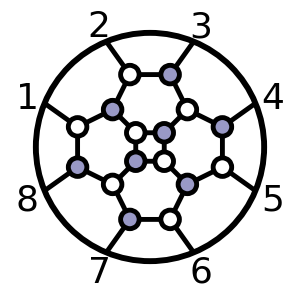

```mathematica
plabicGraph[{6,5,8,7,10,9,12,11}]
```

A graph with vanishing kinematical support:

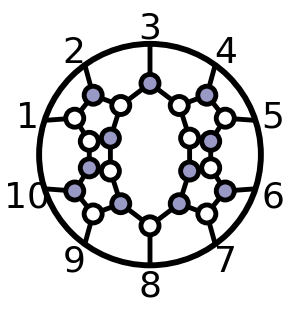

```mathematica
plabicGraph[{5,9,10,7,8,13,14,11,12,16}]
```

An on-shell graph whose physical form includes quartic roots:

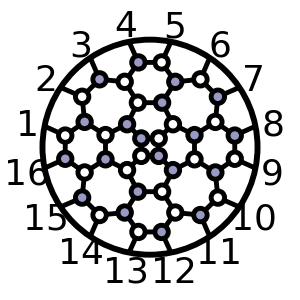

```mathematica
egPerm={11,5,16,10,15,9,20,14,19,13,24,18,23,17,28,22};
plabicGraph[egPerm,chainOption->"cyclic",vertexSize->.25]
```

An on-shell graph whose physical form includes quintic roots:

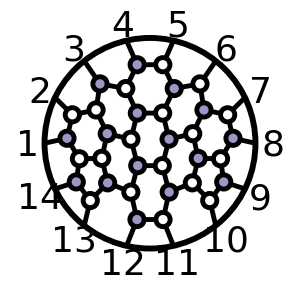

```mathematica
egPerm={6,5,13,12,11,9,10,18,17,15,14,22,16,21};
plabicGraph[egPerm,chainOption->"cyclic",rotation->3,edgePower->3.7,angle->-π/14,vertexSize->.27]
```

A graph with five-fold symmetry:

```mathematica
egPerm={6,5,10,9,8,13,12,11,16,15,14,19,18,17,22};
plabicGraph[egPerm,chainOption->"cyclic",vertexSize->.227,angle->-2π/15,edgePower->7,fontSize->26,labelSpacing->.4,verbose->False]
```

An on-shell graph whose physical form involves 34th-degree roots:

```mathematica
egPerm={9,8,7,21,20,14,13,12,26,25,19,18,17,31,30,24,23,22,36,35};
plabicGraph[egPerm,chainOption->"cyclic",angle->π/20,labelSpacing->.4,fontSize->36,vertexSize->0.195,lineThickness->4.5,imageSize->500,LRarrowSpacing->.135,LRarrowHeadSize->0.045,LRpathThickness->4.5,LRpathDistance->.225,curveParameters->{0.375,0.55},LRpaths->"All",verbose->False]
```

The on-shell graph used for the logo of the positroids package:

```mathematica
egPerm={37,6,40,19,8,42,11,45,34,13,47,16,50,29,18,52,21,55,44,23,57,26,60,39,28,62,31,65,54,33,67,36,70,49,38,72,41,75,64,43};
Fold[Function[{ephPerm,number},Block[{bdy},bdy=Set[boundaryTransposition[ephPerm,"custom"],{Mod[#1+number *5,40,1],rotate[number*5][#2]}&@@boundaryTransposition[rotate[-number*5][ephPerm]]];bdy[[2]]]],egPerm,Range[0,dimension[egPerm]]];
plabicGraph[egPerm,chainOption->"custom",edgePower->1.9,labelSpacing->.35,fontSize->26,vertexSize->0.175,radius->6,lineThickness->3.,angle->-π/20,imageSize->600,LRarrowSpacing->.035,LRarrowHeadSize->0.03,LRpathThickness->3.5,LRpathDistance->.225,curveParameters->{0.305,0.65},LRpaths->"All",verbose->False]
```

## On-Shell Functions and Scattering Amplitudes

### Scattering Amplitudes in the Grassmannian

#### Tree-amplitude contours obtained by the “default” BCFW recursion scheme

Recall that tree-amplitudes in SYM can be recursed in terms of on-shell graphs according to:

Importantly, notice that the scattering-amplitudes appearing across the “BCFW-bridge” can be recursed in any way whatever. If we choose to always recurse these lower-point amplitudes by attaching the “bridge” to only internal legs, then we obtain the collection of positroid cells given by the function “treeContour[n_,k_]”:

For the 6-point NMHV tree-amplitude:

```mathematica
treeContour[6,3]
```

{{4,5,6,8,7,9},{3,5,6,7,8,10},{4,6,5,7,8,9}}

For the 8-point N^2MHV tree-amplitude:

```mathematica
treeContour[8,4]
```

#### Alternative recursion schemes

Several alternative BCFW recursion schemes can be specified by the positroids package (see the documentation for more information). 
One of these “schemes” is used by the function “randomTreeContour[n_,k_]” which chooses random-legs for the recursion of lower-point amplitudes at all levels.

```mathematica
randomTreeContour[6,3]
randomTreeContour[6,3]
```

{{5,4,6,7,8,9},{4,5,7,6,8,9},{4,5,6,7,9,8}}

{{4,5,6,8,7,9},{3,5,6,7,8,10},{4,6,5,7,8,9}}

#### Counting the number of terms generated by the BCFW recursion relations

The number of non-vanishing contributions to a scattering amplitude generated by BCFW recursion is fixed for tree-level and one-loop. This number is given by the function “termsInBCFW[n_,k_,loop_]” (if “loop” is unspecified, tree-level is assumed):

```mathematica
treeContour[6,3]
termsInBCFW[6,3]
```

```mathematica
Length[treeContour[10,5]]
termsInBCFW[10,5]
```

```mathematica
termsInBCFW[14,7]
```

```mathematica
termsInBCFW[6,3,1]
```

#### Naming terms in the BCFW recursion

Each positroid involved in BCFW tree-level recursion can be named according to the sequence of bridges involved; these names are generated by the function bcfwTermNames[n_,k_]:

```mathematica
bcfwTermNames[6,3]
```

### The Specification of Kinematical Data

Scattering amplitudes are ultimately ‘functions’ of kinematical variables. 
This kinematical data represents the n on-shell (null) four-momenta which satisfy momentum conservation. 
The on-shell condition is that each momentum is null, and momentum conservation is the condition that the momenta sum to zero. 
These two conditions can be simultaneously trivialized by using kinematical variables known as “momentum-twistors”:

#### Sepecifying momentum-twistor data

By far the easiest way to specify kinematical data is in terms of n generic 4-vectors known as momentum-twistors—stored as the global (n×4)-matrix “Zs”. To make sure that the positroids package correctly uses particular momentum-twistors for explicit evaluation, one can use the function “setupUsingTwistors[momentumTwistors_]”:

```mathematica
setupUsingTwistors[RandomInteger[{1,50},{10,4}]];
nice[Transpose[Zs]]
```

The function “setupUsingTwistors[]” defines auxilliary spinor-helicity data—stored globally as the (n×2) matrices Ls and Lbs:

```mathematica
nice/@Transpose/@{Ls,Lbs}
```

#### Specifying spinor-helicity data

Perhaps more familiar to most researchers than momentum-twistors are spinor-helicity variables. These correspond to a pair of (2×n) matrices encoding the spinors “λ” and “λ̃”. The disadvantage of spinor-helicity variables is that momentum-conservation is not manifest; therefore, one must be careful to ensure that any spinor-variables used satisfy λ·λ̃=0.

Like for momentum-twistors, spinor-helicity data can be specified directly using the function “setupUsingSpinors[lamdbas_,lambdaBars_]”:

```mathematica
setupUsingSpinors[
{{-3,5},{2,6},{-2,5},{3,3},{0,-5},{-1,2},{2,0},{2,1}},
{{-97/364,-75/364},{-89/616,221/616},{-17/66,-79/462},{-23/45,-11/63},{-4/75,17/15},{14/5,11/4},{5/2,3/8},{-11/13,11/26}}];
```

This defines the global variables Ls and Lbs for λ and λ̃, respectively; 
in addition, setupUsingSpinors[] defines the global matrix Zs which encodes momentum-twsitors corresponding to the spinors.

```mathematica
nice[Transpose[Zs]]
```

#### Using conveniently-chosen “reference” kinematical data

A particularly convenient set of kinematical data—suitable for most purposes—can be used by calling the function positiveZs[n_]:

```mathematica
positiveZs[16]
nice[Transpose[Zs]]
```

For which the corresponding spinor-helicity variables are:

```mathematica
nice/@Transpose/@{Ls,Lbs}
```

### Evaluation of On-Shell (super-)Functions

#### On-shell functions in momentum space (spinor-helicity variables)

An on-shell graph is associated with a positroid cell C_σ labelled by the permutation σ; the corresponding on-shell function is given by:

When the configuration labeled by σ has precisely (2n-4) degrees of freedom, f_σ is considered an ‘on-shell function’.

If f_σ is a superfunction, it is associated with a pair {f_σ^*,C_σ^*} where f_σ^* is an ordinary function and the matrix C_σ^* encodes all the component-functions according to

```mathematica
egPerm=random[treeContour[8,4]]
{fStar,cStar}=permToResidue[egPerm];
nice/@%
```

{4,6,7,10,8,11,9,13}

{-1/756000,(1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 3 | 4 | 5 | 6 | 7 | 8 | 9
0 | 1 | -2 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1/2 | -4 | 5/2 | 0 | 0)}

Thus, the component of the superfunction labeled by egPerm proportional to ((η̃)_1)^4((η̃)_3)^4((η̃)_5)^4((η̃)_7)^4 would be:

```mathematica
fStar*Power[Det[cStar[[All,{1,3,5,7}]]],4]
```

This component can also be extracted using  superComponent[component__][superFunction_]:

```mathematica
superComponent[m,p,m,p,m,p,m,p][permToResidue[egPerm]]
```

#### The evaluation of tree-amplitudes in momentum-space

Recall that tree-ampltudes are the combination of many on-shell functions. Evaluating each results in the full-amplitude. 
For example, the component of A_8^(4) proportional to  ((η̃)_1)^4((η̃)_3)^4((η̃)_5)^4((η̃)_7)^4  (the component amplitude A_8(-,+,-,+,-,+,-,+)) 
can be extracted using the function superComponent[component__][superFunction_]:

```mathematica
permToResidue/@treeContour[8,4];
superComponent[m,p,m,p,m,p,m,p]/@%
Total[%]
```

{-1296/875,-6144/875,-48/175,-108/3325,-98304/83125,-12/4375,-64/1125,0,-16/375,-48/5,-16/675,-48/1625,-2048/219375,-64/225,-4/2925,-36864/70525,-4/279,-16/7875,-256/135,-16/27}

-908416/39375

Different recursion schemes generate different 20-term formulae for this same amplitude—e.g.,

```mathematica
permToResidue/@randomTreeContour[8,4];
superComponent[m,p,m,p,m,p,m,p]/@%
Total[%]
```

These can be viewed as (highly non-trivial) 40-term identities among super-functions.

#### The correspondence between the momentum-space and momentum-twistor Grassmannians

On-shell graphs are associated with positroid configurations in what is called the “momentum-space Grassmannian”—here, each vertex in the plabic graph has the interpretation of being a fully on-shell scattering amplitude.

If an on-shell graph is associated with a positroid configuration in G(k+2,n) labeled by σ, there is a corresponding positroid in the "momentum-twistor Grassmannian” G(k,n)  labelled by σ̂. The correspondence between these two cases is generated by the function dualGrassmannian[perm_]:

```mathematica
egMomentumSpaceContour=treeContour[6,3]
egMomentumTwistorContour=dualGrassmannian/@%
```

```mathematica
egMomentumSpaceContour==dualGrassmannian/@egMomentumTwistorContour
```

#### On-shell funcitons in momentum-twistor space

Very similar to the case of spinor-helicity kinematics, on-shell functions are now associated with cells in the momentum-twistor Grassmannian according to:

For f_σ to be an ordinary function, the positroid configuration labeled by σ must have precisely 4k degrees of freedom.

For example, the momentum-twistor dual of the momentum-space function labeled by egPerm would be given by:

```mathematica
egPermDual=dualGrassmannian[egPerm]
{fStarDual,cStarDual}=permToResidue[egPermDual];
nice/@%
```

Thus, the component of the momentum-twistor superfunction labeled by egPermDual proportional to (η_1)^4(η_3)^4 would be:

```mathematica
fStarDual*Power[Det[cStarDual[[All,{1,3}]]],4]
```

This component can also be extracted using  superComponent[component__][superFunction_]:

```mathematica
superComponent[m,p,m,p,p,p,p,p][permToResidue[egPermDual]]
```

### Combinatorics of Kinematical Support

#### The number of isolated solutions to kinematical constraints

For positroid cells with precisely enough degrees of freedom to be fully isolated by the kinematical constraints (those of dimension (2n-4) for spinor-helicity kinematics and those of dimension (4k) for momentum-twistor kinematics), the number of isolated solutions to the kinematical constraints is computed using the function intersectionNumber[perm_]:

```mathematica
egPerm={9,8,7,21,20,14,13,12,26,25,19,18,17,31,30,24,23,22,36,35};
plabicGraph[egPerm]
```

```mathematica
intersectionNumber[egPerm]
```

The following examples illustrate this computation for a number of (less dramatic) on-shell graphs:

#### Exempli gratia: an on-shell graph without kinematical support

```mathematica
egPerm={5,9,10,7,8,13,14,11,12,16};
plabicGraph[egPerm]
```

```mathematica
intersectionNumber[egPerm]
```

We can verify this as follows: for spinor-helicity kinematics,

```mathematica
(*Setup reference kinematics for the number of particles in question*)
positiveZs[Length[egPerm]];
(*Construct a matrix-representative of the positroid cell labeled by egPerm*)
egMat=permToMat[egPerm];
(*Define the kinematical constraint equations, C·λ̃=0 and C^⊥·λ=0.*)kinematicalConstraintEquations=GroebnerBasis[Flatten[{egMat.Lbs,NullSpace[egMat].Ls}],Variables[egMat]];
(*Number of solutions is given by:*)
Length[Solve[#==0&/@kinematicalConstraintEquations]]
```

or, alternatively, using momentum-twistor kienatmics:

```mathematica
(*Construct a matrix-representative of the positroid cell labeled by egPerm*)
egDualMat=permToMat[dualGrassmannian@egPerm];
(*Define the kinematical constraint equations, C·Z=0*)kinematicalConstraintEquations=GroebnerBasis[Flatten[{egDualMat.Zs}],Variables[egDualMat]];
(*Number of solutions is given by:*)
Length[Solve[#==0&/@kinematicalConstraintEquations]]
```

#### Exempli gratia: the four-mass box with two solutions to the kinematical constraints

```mathematica
egPerm={6,5,8,7,10,9,12,11};
plabicGraph[egPerm]
```

```mathematica
intersectionNumber[egPerm]
```

We can verify this as follows: for spinor-helicity kinematics,

```mathematica
(*Setup reference kinematics for the number of particles in question*)
positiveZs[Length[egPerm]];
(*Construct a matrix-representative of the positroid cell labeled by egPerm*)
egMat=permToMat[egPerm];
(*Define the kinematical constraint equations, C·λ̃=0 and C^⊥·λ=0.*)kinematicalConstraintEquations=GroebnerBasis[Flatten[{egMat.Lbs,NullSpace[egMat].Ls}],Variables[egMat]];
(*Number of solutions is given by:*)
Length[Solve[#==0&/@kinematicalConstraintEquations]]
```

or, alternatively, using momentum-twistor kienatmics:

```mathematica
(*Construct a matrix-representative of the positroid cell labeled by egPerm*)
egDualMat=permToMat[dualGrassmannian@egPerm];
(*Define the kinematical constraint equations, C·Z=0*)kinematicalConstraintEquations=GroebnerBasis[Flatten[{egDualMat.Zs}],Variables[egDualMat]];
(*Number of solutions is given by:*)
Length[Solve[#==0&/@kinematicalConstraintEquations]]
```

#### Exempli gratia: an example with four points of kinematical support

```mathematica
egPerm={11,5,16,10,15,9,20,14,19,13,24,18,23,17,28,22};
plabicGraph[egPerm]
```

```mathematica
intersectionNumber[egPerm]
```

We can verify this using momentum-twistor kinematics:

```mathematica
(*Setup reference kinematics for the number of particles in question*)
positiveZs[Length[egPerm]];
(*Construct a matrix-representative of the positroid cell labeled by egPerm*)
egDualMat=permToMat[dualGrassmannian@egPerm];
(*Define the kinematical constraint equations, C·Z=0*)kinematicalConstraintEquations=GroebnerBasis[Flatten[{egDualMat.Zs}],Variables[egDualMat]];
(*Number of solutions is given by:*)
Length[Solve[#==0&/@kinematicalConstraintEquations]]
```

### Identities Among On-Shell Functions

#### The generation of identities among on-shell functions

Consider any positroid cell with precisely enough degrees of freedom to be fully isolated by the kinematical constraints (those of dimension (2n-4) for spinor-helicity kinematics and those of dimension (4k) for momentum-twistor kinematics):

```mathematica
egPerm=treeContour[8,4][[7]]
plabicGraph[egPerm,chainOption->"cyclic"]
```

An identity involving the cell labeled by egPerm can be generated as the boundary[] of any of the cells from those in inverseBoundary[egPerm]:

```mathematica
egIdentitySeed=random[inverseBoundary[egPerm]]
egIdentityList=Select[boundary[egIdentitySeed],nonSingularQ]
plabicGraph/@egIdentityList
```

(Notice that we have selected only those cells which are “non-singular”—tested by the function nonSingularQ[]; a “non-singular” cell is one for which intersectionNumber[]>0.)

The cells involved in this boundary each represent superfunctions, which can be evaluated for particular kinematical data using “permToResidue[]” as described above:

```mathematica
egIdentityFunctions=permToResidue/@egIdentityList;
nice/@%
```

Of course, being an identity among explicit functions, signs are dictated by the orientations of the cells involved. These can be found using the function identitySigns[permutationList_]:

```mathematica
egIdSigns=identitySigns[egIdentityList]
```

We can then verify this identity as before for any component using superComponent[component__][superFunction_]:

```mathematica
egComponent=Normal[SparseArray[#->m&/@random[preferredGauge/@egIdentityList],Length[egIdentitySeed],p]]
superComponent[Sequence@@egComponent]/@egIdentityFunctions;
%*egIdSigns
Total[%]
```

#### A more complicated identity among on-shell functions:

Below, we repeat the exercise above for a more complex identity—one involving the four-mass box:

```mathematica
egIdentitySeed={4,7,6,9,8,10,11,13}
egIdentityList=Select[boundary[egIdentitySeed],nonSingularQ]
plabicGraph/@egIdentityList
```

We can see that this identity involves an object with more than one point of kinematical support by checking:

```mathematica
intersectionNumber/@egIdentityList
```

As before, we can convert each of these positroid cells to their corresponding superfunctions using “permToResidue[perm_]”

```mathematica
egIdentityFunctions=Simplify@(permToResidue/@egIdentityList);
nice/@%
```

(When the function “permToResidue[]” is evaluated for a cell with multiple points of kinematical support, it returns a list of super-functions—one for each isolated solution.)

As before, we can find the necessary signs associated with the identity among these cells using identitySigns[permList_]:

```mathematica
egIdSigns=identitySigns[egIdentityList]
```

And we can verify the identity for any randomly-chosen component of the superfunctions involved:

```mathematica
egComponent=Normal[SparseArray[#->m&/@random[preferredGauge/@egIdentityList],Length[egIdentitySeed],p]]
superComponent[Sequence@@egComponent]/@egIdentityFunctions;
Simplify[%*egIdSigns]
Total[%]
```